# THE MULTISCALE NATURE OF DEFORMATION AND METAMORPHISM

# Data, Patterns, Dynamics, Prediction

Alison Ord

Mentor  Flip Phillips

## Background

Hobbs & Ord (2015) is concerned with the processes that operate during the deformation and metamorphism of rocks in the crust and upper lithosphere of the Earth. The deformation and metamorphism of rocks involves structural rearrangements of elements of the rock at the microscale by processes such as mass diffusion, dislocation slip and climb, grain-boundary migration and fracturing at the same time as chemical reactions proceed. In some instances infiltrating fluids introduce or remove chemical components and may influence mechanical properties through changes in mineralogical composition, fluid pressure or temperature. At the same time, heat is added to or removed from the system depending on the surrounding tectonic environment. Such mechanisms do not operate independently of each other but are coupled so that each process has feedback influences on the others leading to structures and mineral assemblages that do not develop in the uncoupled environment.

Its contents are represented by this Word Cloud.

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School"]
image=Import["hobbs&ord2015WordCloud.jpg"];
imageshow=ImageResize[image,Large]
```

C:\Users\Alison\Documents\Personal\Wolfram Summer School

-Graphics-

This computational essay is a first step towards developing the application of the tools of nonlinear dynamics to measuring rocks, to measuring the structural architectures which result from processes interacting and developing in a coupled environment.

## Vision

The vision for mathematica is of moving a cursor through (x, y, z) coordinates for the surface of a deformed, folded rock and to watch data driven analyses change in different windows including : spatial attractors, wavelet transforms, singularity spectra, Hurst exponents, recurrence plots (including the ability for cross - and joint - recurrence plots and their quantitative analysis), Fourier transforms, recurrence histograms, networks, and sparsely determined nonlinear determinations of the differential equations describing the data.

## Step 1

Are folded rocks a snapshot of a nonlinear dynamic system? When layered rocks are shortened during tectonic events, the most obvious structures formed are folds. Folding of layered rocks causes a change in geological structure that can lead to a fundamental modification of the mechanical and hydraulic properties of the rock mass across several orders of magnitude in length - typically from the millimetre to the kilometre-scale. 

The understanding of how, why and on which scale folding occurs therefore has fundamental implications for problems in geology and engineering, including prediction of the form and location of hydrocarbon accumulations, salt domes, groundwater flow, mineralization, and rock slope stability.

We have prepared three dimensional models of natural fold systems using photogrammetry and we explore the multifractal geometry using wavelet transforms and recurrence quantification in order to delineate the dynamics of naturally folded systems.

## The Data

### Surfaces of folded rocks

First we see a multiply deformed rock with porphyroblasts from Rum Jungle in Australia.

-Graphics-

It is then photographed from multiple angles, and the images collated and analysed within CloudCompare. This image shows interpreted cloud of points, with a single line through the points denoting the data collected, and shown in cross section in the following figure.

-Graphics-

Here is another multiply folded rock, this time from Broken Hill in Australia. First, we look at the rock, sitting on a structured page used for collating the photographic images.

-Graphics-

Second, we see the cloud of points for that system, derived from the photo collection.

-Graphics-

Third, we have the cloud of points just of the rock, followed by a section through the rock cloud,

-Graphics-

and an imported version of the cross section.

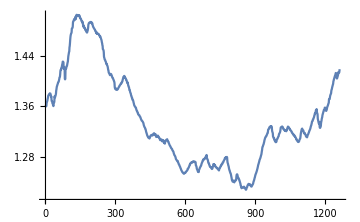

## The Analyses

### Spatial attractors

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\BHill images"];
```

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\BHill images

C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\BHill images

Here we show the spatial attractor for the data with a lag of 20, in various styles.

```mathematica
m=Import["Section contour #4 lag 1.xlsx",{"Sheets",3}];
```

```mathematica
ListPointPlot3D[m,DataRange->Automatic,ColorFunctionScaling->True,ColorFunction->"Rainbow",Axes->True,PlotRange->All,BoxRatios->{1,1,1},AxesLabel->{t,t+20,t+40},ImageSize->Small]
```

-Graphics3D-

```mathematica
junk=BSplineCurve[{m}];
Tube[junk];
Graphics3D[{Orange,Specularity[White,10],Tube[junk,.002]},Axes->True,PlotRange->All,Boxed->True,BoxRatios->{1, 1, 1},BoxStyle->Directive[Dashed,Gray],Background->Black,LabelStyle->Directive[Black,Bold],AxesLabel->{i, i+20,i+40},ViewPoint->{-2,2,0},ImagePadding->4,ImageSize->Small]
```

-Graphics3D-

### Wavelet transforms

ContinuousWaveletData[…]

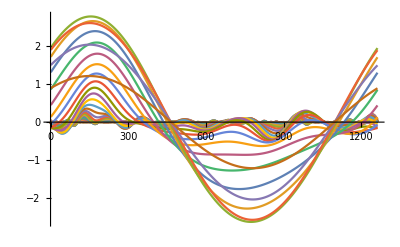

```mathematica
cwd=ContinuousWaveletTransform[datalist,WaveletScale->1]
cwd[All,"Values"];
recwd=Re[%];
cwd[{"WaveletScale","Octaves","Voices"}];
ListLinePlot[recwd,PlotRange->All]
```

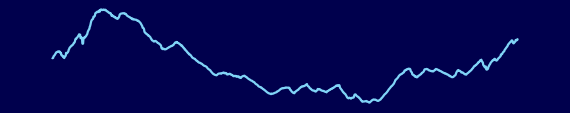
-Graphics-
-Graphics-

```mathematica
cf[x_]:=Blend[{RGBColor[0.,0.,0.3],RGBColor[0.,0.,0.5],RGBColor[0,0.1,0.5],RGBColor[0,0.2,1],RGBColor[0,0.5,1],RGBColor[0.2,0.7,1],RGBColor[0.5,0.8,1],RGBColor[0.5,.9,.9],RGBColor[0.5,1.,0.9],RGBColor[0.7,1,0.7],RGBColor[0.8,1,0.5],RGBColor[1,1,0],RGBColor[1,0.8,0],RGBColor[1,0.5,0],RGBColor[1,.25,0],RGBColor[1,.1,0.],RGBColor[1,.0,0.],RGBColor[.9,.0,0.],RGBColor[0.8,0.,0.],RGBColor[0.5,0.,0.],RGBColor[.25,0.,0.],RGBColor[0.1,0,0]},x];
Column[{ListLinePlot[datalist,Axes->None,ImageSize->570,AspectRatio->0.2,PlotRangePadding->None,PlotRange->All,Background->cf[0],PlotStyle->cf[0.3]],WaveletScalogram[cwd,ColorFunction->(cf[#]&),Axes->True,ImageSize->570,PlotRangePadding->None,Ticks->Full]},Spacings->0.2]
```

```mathematica
ListPlot3D[recwd,ColorFunction->"DarkRainbow",AxesLabel->{"depth","scale"},Mesh->None,PlotRange->All]
```

-Graphics3D-

### Singularity spectra

The singularity spectra are presently created using Last Wave. See Bacry et al. (1993) and Arneodo et al. (2008).

```mathematica
SetDirectory["C:\\Users\\Alison\\Documents\\Personal\\Wolfram Summer School\\Projects\\BHill images"];
imageshow=ImageResize[Import["rock4zSingSpec.jpg"],Medium]
```

-Graphics-

### Recurrence quantitative analysis

## Initialise

Load FP’s RQA package

```mathematica
gitHubDir=ResourceFunction["NotebookRelativePath"][{"..","..","..","RQA","RQA"}]
```

C:\Users\Alison\Documents\GitHub\WSS2019-ao\Final Project\Drafts\..\..\..\RQA\RQA

```mathematica
Get[FileNameJoin[{gitHubDir,"RQA.wl"}]]
```

```mathematica
?RQA`*
```

```mathematica
(* <<RQA` *)
```

The package is built on the equations expressed in Webber and Marwan (2015).

## Find and load the data

• try SemanticImport for easier import of various types of data. Bob Nachbar   Trial with *.xlsx in ComputationEssay5.nb or whatever

```mathematica
data=Flatten[SemanticImport[ResourceFunction["NotebookRelativePath"][{"..","Data","rock4z.dat"}]]];
```

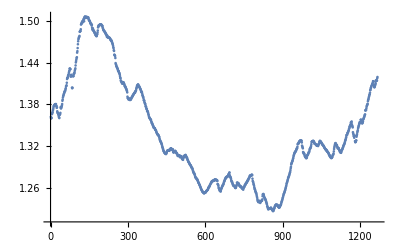

```mathematica
ListPlot[data]
```

```mathematica
data=Flatten[Import[ResourceFunction["NotebookRelativePath"][{"..","Data","rock4z.dat"}]]];
```

```mathematica
(* data=Flatten[Import[ResourceFunction["NotebookRelativePath"][{"..","Data","r30datab.dat"}]]] ; *)
```

data=Flatten[Import["C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\Rule30Results\r30datab.dat"]]

We start by using the data from the same folded rock, or to Rule30, to which we applied the nonlinear tools of spatial attractor, wavelet transform (2D and 3D), Hurst exponents, singularity spectrum (not yet in mtca), and so on.

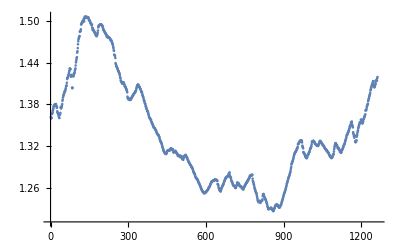

```mathematica
ListPlot[data]
```

We create a time series in the form required by mtca.

```mathematica
ds=RQAMakeTimeSeries[data,1,1]
```

TimeSeries[…]

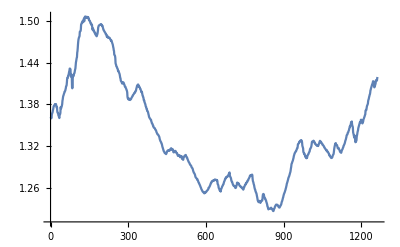

```mathematica
ListLinePlot[ds]
```

Trial some predictions based on existing mtca functions

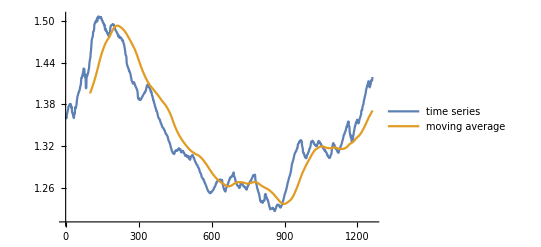

```mathematica
avg=MovingAverage[ds,100];
ListLinePlot[{ds,avg},PlotLegends->{"time series","moving average"}]
```

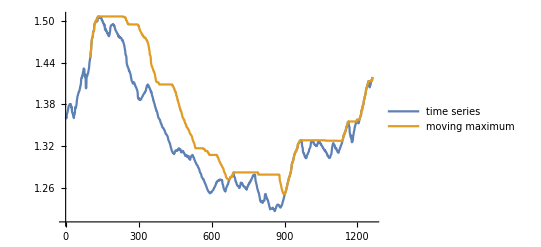

```mathematica
max=MovingMap[Max,ds,100];
ListLinePlot[{ds,max},PlotLegends->{"time series","moving maximum"}]
```

```mathematica
dsm=TimeSeriesModelFit[ds]
```

TimeSeriesModel[…]

Use TimeSeriesForecastpaclet:ref/TimeSeriesForecast to forecast the next 1000 values in the time series:

```mathematica
dsf=TimeSeriesForecast[dsm,{1000}];
```

Plot the time series along with the forecast:

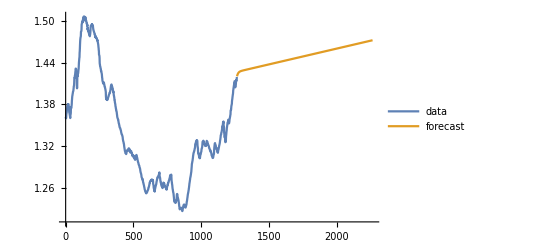

```mathematica
ListLinePlot[{ds,dsf},PlotLegends->{"data","forecast"}]
```

```mathematica
eproc=TimeSeriesModelFit[ds,{"SARIMA",12}]["Process"]
```

SARIMAProcess[-2.37682×10^-7,{0.41765,0.19998},1,{},{12,{-0.0917179},1,{-0.846865}},2.3812×10^-6]

```mathematica
forecast=TimeSeriesForecast[eproc,ds,{1000}];
```

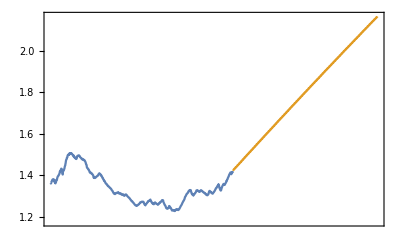

```mathematica
DateListPlot[{ds,forecast},Joined->True]
```

## Estimate the lag and embedding dimensions for the data

The lag is first estimated-

```mathematica
lag=RQAEstimateLag[ds]
```

305.726

However, a lag of 10 was used in previously published work (Ord&Hobbs, 2018; Ord et al., 2018) so that is what we will use here.

```mathematica
lag=10
```

10

The embedding dimension of the system is then estimated. The result below suggests a dimension of 3.

```mathematica
RQAEstimateDimensionality[ds,lag]
```

4.72984×10^-7

{Null,{{{2,0.40655,1262,4.72984×10^-8,1252,1.41325×10^-6},{3,0.0990338,1252,1.41325×10^-6,1242,2.94388×10^-6},{4,0.023539,1242,2.94388×10^-6,1232,4.36527×10^-6}}}}

```mathematica
embedding=RQAEmbed[ds,3,lag]
```

TimeSeries[…]

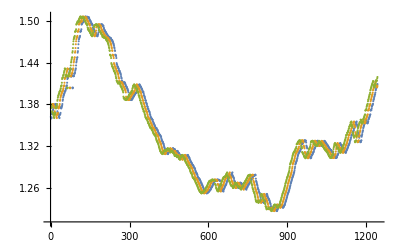

```mathematica
ListPlot[embedding]
```

## Plot the 3D spatial attractor

embedding is now a list of 3 columns of data, off set by the lag of 10, and we plot these in three dimensions, with the axes representing t, t+10, t+20

```mathematica
ParametricPlot3D[embedding[t],{t,1,650}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222},PlotStyle->{Orange,Specularity[White,10]},ViewPoint->{Left,Top}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222},PlotStyle->Directive[Green,Opacity[0.8],Specularity[White,20]],ViewPoint->{Left,Bottom}]
```

-Graphics3D-

## Interrogate the neighbours

These give you information on the neighbours, nearestneighbours and neighbours, but what is it you really need to know? Number of nearest neighbours? & don’t you normally (in VRA) search for these earlier while determining the dimensionality?

```mathematica
rn=RQANeighbors[embedding];
```

```mathematica
rnn=RQANearestNeighbors[embedding];
```

```mathematica
rnd=RQANeighborDistances[embedding];
```

## Calculate the distance map and the recurrence map

Webber (2012) numerical examples provide explicit step-by-step details on how input vectors (data) are delayed, embedded, normed, and rescaled
to define elements (distances) in the distance matrix (DM). Also described is how the recurrence matrix (RM) is derived from the DM by selecting only those recurrent points with distances falling within a selected RADIUS. Understanding of these simple examples should remove the mathematical mystery behind the basis of recurrence quantification analysis which simply finds patterns among recurrent points according to objective rules.
README_2012.PDF

Webber Chap 2.pdf the radius parameter implements a cut-off limit (Heavyside function) that transforms the distance matrix
(DM) into the recurrence matrix (RM). That is, all (i, j) elements in DM with distances at or below the RADIUS cutoff are included in the
recurrence matrix (element value = 1), but all other elements are excluded from RM (element value = 0). Note carefully that the RM
derives from the DM, but the two matrices are not identical.

FlipPhillips (pers.comm. 2019) Let us now look at the distance map. 1) recurrence maps are computed from distance maps.
2) distance maps are constant for any given embedding
3) recurrence maps are distance maps thresholded on a given distance
3a) If you don’t supply a threshold radius in the recurrence map command one will be computed for you (mean of all distances in the map)
4) ‘recurrence maps’ as created by your/my program a) use a strange distance measure that seems to be 100x the ‘real’ distance in Euclidean space and b) are a _combination_ of the distance map thresholded by the recurrence map.

Using these values for the lag of 10 and for the embedding dimension of 3, we can now calculate the distance map

```mathematica
dm=RQADistanceMap[embedding];
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue]
```

-Graphics-

The minimum and maximum are  determined to be 0 and 0.224875 - for rock4z
0 and 17251 for Rule30!

```mathematica
MinMax[dm]
```

{0.,0.224875}

find its dimensions

```mathematica
Dimensions[dm]
```

{1242,1242}

and the first number in the expression, that is, in the list of dimensions

```mathematica
First[Dimensions[dm]]
```

1242

Using these values for the lag of 10 and for the embedding dimension of 3, we can now calculate the recurrence map

```mathematica
Mean[Flatten[dm]]
```

0.0340171

So the automatic radius for Rule30 is 3462.13 while the automatic radius for rock4z is 0.0340171

```mathematica
rm=RQARecurrenceMap[embedding];
```

find its dimensions

```mathematica
Dimensions[rm]
```

{1242,1242}

and the first number in the expression, that is, in the list of dimensions

```mathematica
First[Dimensions[rm]]
```

1242

The recurrence map may be plotted

```mathematica
MatrixPlot[rm,DataReversed->{True,False},PlotRange->All,ColorFunction->(RGBColor[1-#,#,1/2]&)]
```

-Graphics-

The minimum and maximum of the recurrence are determined to be 0 and 1 respectively.

```mathematica
MinMax[rm]
```

{0,1}

## Calculate the RQA measures; compare with those using Webber’s RQA software

```mathematica
N[RQARecurrence[rm]]
```

0.680771

This compares with %REC=40.2 which is the result from Webber’s RQA for embedding dimension of 3 and a lag of 10

```mathematica
N[RQADeterminism[rm]]
```

0.999567

%DET=99.9 Result from RQA

```mathematica
N[RQALaminarity[rm,3]]
```

0.999178

%LAM=100 Result from RQA

```mathematica
N[RQATrappingTime[rm]]
```

220.737

TT=121.8 Result from RQA

```mathematica
N[RQATrend[rm]]
```

General::munfl: Exp[-3203.58] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1413.91] is too small to represent as a normalized machine number; precision may be lost.

-30.6973

Trend -56.4 Result from RQA

```mathematica
N[RQAEntropy[rm]]
```

8.02657

Entropy 7.6 Result from RQA

```mathematica
N[RQAChaos[rm]]
```

0.000805802

Result from RQA ? 1/DMAX

First pass code for calculating DMAX. It should be easy to derive from DET as only wanting the maximum of the length segments of the diagonal; don’t need to divide that number by the total number recurrent plots. You can change DMAX by changing the first part of the Range. For example, for @Range[500,w-1] DMAX=319, and for @Range[1000,w-1] DMAX=134

```mathematica
RQADmax[rm_,thresh_:2]:=Module[{ut,w,diags,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
diags=Diagonal[ut,#]&/@Range[1,w-1];
segLens=segmentLengths[diags,thresh];
lens=Total/@segLens;
Max[segLens]
]/;SquareMatrixQ[rm]
```

why has this stopped working? changed threshold to 3 - it worked. changed threshold to 2 - it worked. ? !

```mathematica
RQADmax[rm,2]//N
```

1241.

DMAX 1241 Result from RQA

1/DMax = ‘chaos’ as expected. ‘chaos’ is the maximum Lyapunov exponent. Note that the 2 here is the magnitude of the line required to be stated in the Webber code.

```mathematica
1/%
```

0.000805802

=1/chaos - as expected

Similarly here for VMAX. The segment lengths are for the verticals.

```mathematica
RQAVmax[rm_,thresh_:2]:=Module[{ut,verts,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
verts=Transpose[ut];
segLens=segmentLengths[verts,thresh];
lens=Total/@segLens;
Max[segLens]
]/;SquareMatrixQ[rm]
```

```mathematica
RQAVmax[rm,2]
```

889

VMAX -592 Result from RQA

```mathematica
RQADetnew[rm_,thresh_:2]:=Module[{ut,w,diags,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
diags=Diagonal[ut,#]&/@Range[1,w-1];
segLens=segmentLengths[diags,thresh];
lens=Total/@segLens;
nRP=Total[Flatten[ut]];
Total[lens]/nRP]/;SquareMatrixQ[rm]
```

```mathematica
RQADetnew[rm,2]//N
```

0.999567

```mathematica
RQARecurnew[rm_]:=Module[{ut,w,nMax,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
nMax=(w (w-1)/2);
nRP=Total[Flatten[ut]];
nRP/nMax]/;SquareMatrixQ[rm]
runLength[list_]:={First[#],Length[#]}&/@Split[list]
segmentLengths[m_,tLen_:2]:=Module[{rl,selFun,n},rl=runLength/@m;
selFun=Select[#[[1]]==1∧#[[2]]≥tLen&];
(selFun/@rl)/.{{}->{0},{1,n_}->n}]
```

```mathematica
RQARecurnew[rm]//N
```

0.680771

Marwan&Webber Equation 1.11

```mathematica
RQARatio=N[RQADeterminism[rm]]/N[RQARecurrence[rm]]
```

1.46829

```mathematica
ListPlot[data]
```

-Graphics-

```mathematica
Manipulate[ListLinePlot[Take[data,{x,x+200}]],{{x,1},1,1200},SaveDefinitions->True,FrameLabel->"saved"]
```

```mathematica
ds["Properties"];
```

```mathematica
dsw=TimeSeriesWindow[ds,{1,1242}]
```

TimeSeries[…]

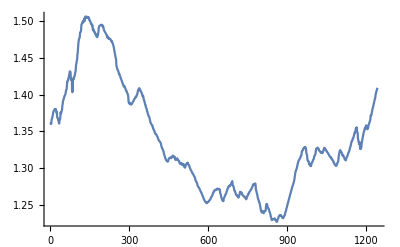

```mathematica
Plot[dsw[t],{t,dsw["FirstTime"],dsw["LastTime"]},PlotRange->All]
```

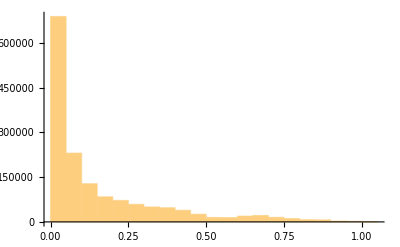

```mathematica
Histogram[Rescale[Flatten[dm]]]
```

```mathematica
Mean[Differences[ds["Times"]]]
```

1

CorrelationFunctionpaclet:ref/CorrelationFunction[data,hspec] estimates the correlation function at lags hspec from data.
hspec        | {τ_min,τ_max} | unit spaced from τ_min to τ_max

```mathematica
f=CorrelationFunction[ds,{1,1242}]
```

TimeSeries[…]

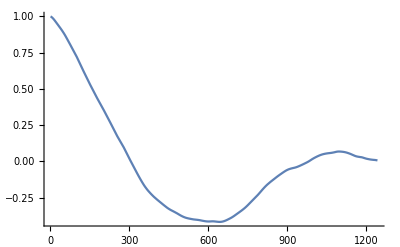

```mathematica
Plot[f[t],{t,1,1242},PlotRange->All]
```

```mathematica
FindRoot[f[t],{t,1}]
```

{t→305.726}

```mathematica
Fourier[data];
```

```mathematica
MinMax[Abs[Fourier[data]]]
```

{0.000064906,47.5676}

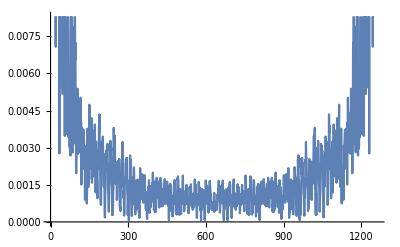

```mathematica
ListLinePlot[Abs[Fourier[data]],PlotRange->Automatic]
```

This is equivalent to the original estimate of the lag!

```mathematica
embedLag=RQAEstimateLag[ds]
```

305.726

```mathematica
RQAEstimateDimensionality[ds,embedLag]
```

4.72984×10^-7

{Null,{{{2,0.35251,1262,4.72984×10^-8,956,1.38088×10^-6},{3,0.0661538,956,1.38088×10^-6,650,2.69822×10^-6},{4,0.0116279,650,2.69822×10^-6,344,4.23066×10^-6}}}}

## Time Series Epochs start here

RQATimeSeriesEpochs[ts_,wid_,overlap_]:=
Table[TimeSeriesWindow[ts,{t0,t0+wid}],{t0,ts[“FirstTime”],ts[“LastTime”]-wid,overlap}]

```mathematica
e=RQATimeSeriesEpochs[dsw,200,50];
```

How will you find and plot these windows on the original recurrence map?

```mathematica
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue,Frame->True,FrameTicks->{{{1,51,101,151,201,401,601,801,1001,1201},{1,51,101,151,201,401,601,801,1001,1201}},{{1,51,101,151,201,401,601,801,1001,1201},{1,51,101,151,201,401,601,801,1001,1201}}}]
```

-Graphics-

```mathematica
Head[%];
```

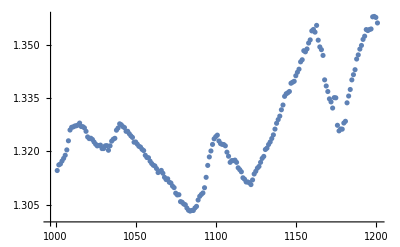

```mathematica
ListPlot[e[[-1]]]
```

If TimeSeriesEpochs defines the windows, how do you talk to the windows, compute the RQA, plot them?
6July2019 Getting there

So for each part of list e, calculate the following, with ds replaced by that part of the list:

```mathematica
embedding=RQAEmbed[e[[-1]],3,lag]
```

TimeSeries[…]

```mathematica
rm=RQARecurrenceMap[embedding];
```

```mathematica
RQARecurrence[rm]//N
```

0.621731

```mathematica
RQADeterminism[rm]//N
```

0.997235

```mathematica
RQALaminarity[rm,3]//N
```

0.997334

```mathematica
RQATrappingTime[rm]//N
```

42.1375

```mathematica
RQATrend[rm]//N
```

-226.382

```mathematica
RQAEntropy[rm]//N
```

6.03963

```mathematica
RQAChaos[rm]//N
```

0.00555556

```mathematica
RQADmax[rm,2]//N
```

180.

```mathematica
RQAVmax[rm,2]//N
```

120.

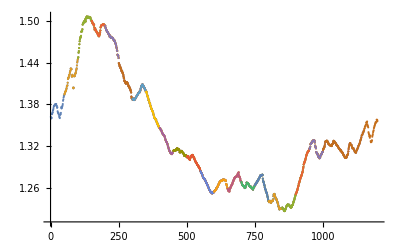
Map[-Graphics-]

```mathematica
Map[ListPlot[e]]
```

```mathematica
len=Length[e]
```

21

```mathematica
e[[3]]//N
```

TimeSeries[…]

```mathematica
Do[ListPlot[e[[i]]],{i,len}]
```

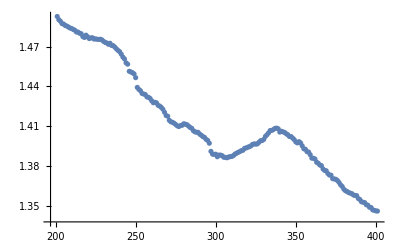

```mathematica
ListPlot[e[[5]]]
```

for each part of list e you need to calculate:
1. RQAEmbed[e[[part]],3,lag]
2. RQARecurrenceMap[RQAEmbed[e[[part]],3,lag]]
3. all the RQAs

copied from Flip Phillips epochs for alison.nb

```mathematica
eps=RQATimeSeriesEpochs[dsw,400,200];
```

So the following estimates the lag for each of the time series, eps 
Mappaclet:ref/Map[f,expr] or f/@expr   applies f to each element on the first level in expr.

```mathematica
Head[eps]
```

List

```mathematica
taus=Map[RQAEstimateLag,eps]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{89.5272,139.201,146.776,146.776,146.776}

```mathematica
Mean[%]
```

133.811

RQAEmbed::usage=”RQAEmbed[ts,dims,tau] but why.”
#   Slot   represents the first argument supplied to a pure function. 
embeds as follows gives a list of TimeSeries, each of which it should be possible to address and plot separately.

```mathematica
embeds=Map[RQAEmbed[#,3,30.0]&,eps];
```

```mathematica
embeds=Map[RQAEmbed[#,3,10.0]&,eps];
```

```mathematica
Head[embeds]
```

List

N doesnt, and won’t, work here as it gives the numerical value of an expression, it does not count things.

```mathematica
N[embeds];
```

These bits of code successfully plot coloured squares for each epoch for the distance map

Mappaclet:ref/Map[f,expr] or f/@expr   applies f to each element on the first level in expr.

```mathematica
maps=RQADistanceMap/@embeds;
```

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None]&/@maps;
```

Since the recurrence map is calculated for each epoch, the colour ranges are slightly different from the main recurrence map.

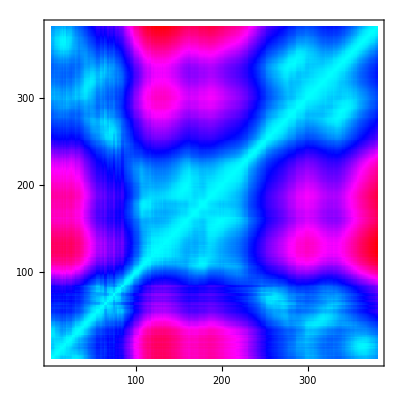
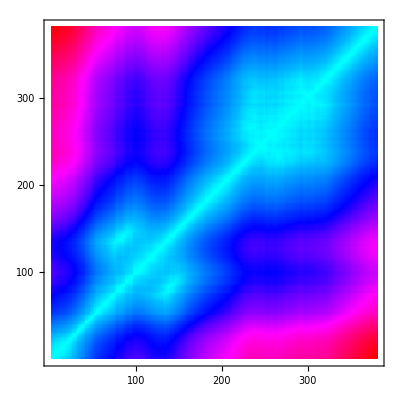
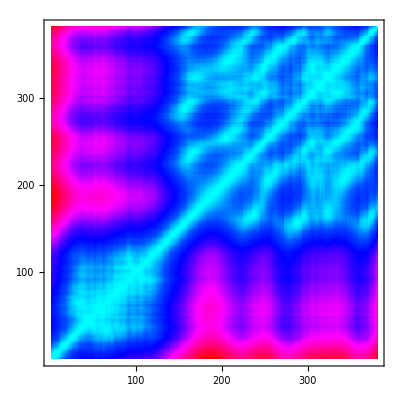
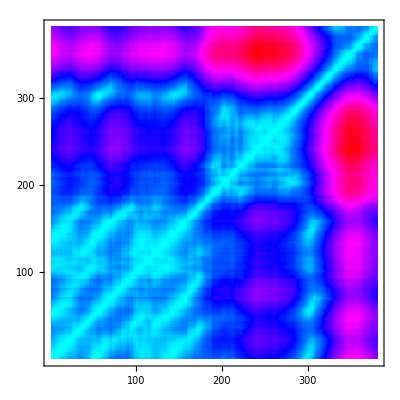
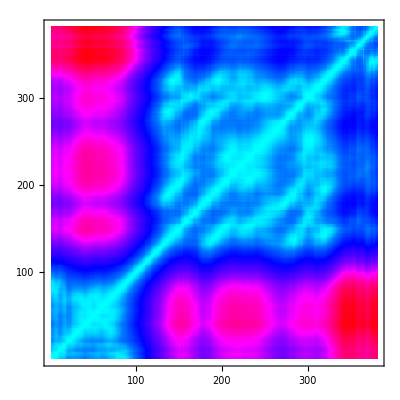

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->Automatic,ColorFunction->Hue]&/@maps
```

```mathematica
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue,Frame->True,FrameTicks->{{{1,51,101,151,201,401,601,801,1001,1201},{1,51,101,151,201,401,601,801,1001,1201}},{{1,51,101,151,201,401,601,801,1001,1201},{1,51,101,151,201,401,601,801,1001,1201}}}]
```

-Graphics-

```mathematica
(* numbers=RQARecurrenceMap[#,.01]&/@embeds; *)
```

```mathematica
numbers=RQARecurrenceMap[#]&/@embeds;
```

```mathematica
Length[embeds]
```

5

and for the recurrence map

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None,ColorFunction->Hue]&/@numbers;
```

```mathematica
N[RQADeterminism/@numbers]
```

{0.999192,0.998981,0.999342,0.999415,0.999956}

```mathematica
N[RQALaminarity/@numbers]
```

{0.999326,0.999469,0.999478,0.999657,0.999934}

```mathematica
N[RQATrappingTime/@numbers]
```

{72.3577,99.9384,108.027,79.1933,115.202}

```mathematica
N[RQATrend/@numbers]
```

General::munfl: Exp[-1023.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1181.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1000.95] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-120.639,-123.385,-124.391,-80.6275,-116.472}

```mathematica
N[RQAEntropy/@numbers]
```

{6.59974,7.0803,7.2437,6.9317,7.73251}

```mathematica
N[RQAChaos/@numbers]
```

{0.00263158,0.00263158,0.00263158,0.00263158,0.00263158}

```mathematica
N[RQADmax/@numbers]
```

{380.,380.,380.,380.,380.}

```mathematica
1/N[RQAChaos/@numbers]
```

{380.,380.,380.,380.,380.}

```mathematica
N[RQAVmax/@numbers]
```

{209.,185.,272.,299.,261.}

```mathematica
TabView[{"Rec"->ListLinePlot[N[RQARecurrence/@numbers]],"Det"->ListLinePlot[N[RQADeterminism/@numbers]],"Lam"->ListLinePlot[N[RQALaminarity/@numbers]],"Trap"->ListLinePlot[N[RQATrappingTime/@numbers]],"Trend"->ListLinePlot[N[RQATrend/@numbers]],"Entropy"->ListLinePlot[N[RQAEntropy/@numbers]],"Dmax"->ListLinePlot[N[RQADmax/@numbers]],"Vmax"->ListLinePlot[N[RQAVmax/@numbers]],"Chaos"->ListLinePlot[N[RQAChaos/@numbers]]}]
```

General::munfl: Exp[-1023.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1181.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1000.95] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

123456789

Example from mtca! Show some famous cellular automata in a TabViewpaclet:ref/TabView:

```mathematica
TabView[Table[Row[{"rule ",r}]->ArrayPlot[CellularAutomaton[r,{{1},0},40]],{r,{30,90,126,150}}]]
```

1234

## To do notes

8 July 2019
• modify the existing epoch plots so that the x axis represents the absolute position within the timeseries, not just the position within the epoch.
• Work out how to interrogate a particular RQA while moving through the data - 12 little recurrence plots look very pretty - but how about when you interrogate 120,000 points, 260,000 points, 1 trillion points?
•  A related problem - within the recurrence plot for all data (or at least the data you wish to explore), how do you visualise/manipulate a window representing TimeSeriesEpochs moving up and down the LOI line of ? of the main recurrence plot with the recurrence plot representing the epoch showing up on the side?
•  Clean up the mtca code you have been using for calculating Hurst exponents.

#### Future Work

### Discovery of physics from data

#### Application of Brunton’s Matlab SINDy code using Octave

% Copyright 2018
% Code by Alison Ord based on Brunton et al. 2015
% based on rocks analysed in 2017/2018   JSG   PhilTransA

clear all, close all, clc
figpath = ‘../figures/’;
addpath(‘./utils’);
addpath(‘./data’);

%% generate Data
polyorder = 5;
usesine = 0;

n = 3;

% Integrate
% you need to load x as well as dx
load -ascii rock4z_x.txt
x=99*rock4z_x;
%N = length(x);
load -ascii rock4z_dx.txt
dx=217*rock4z_dx;
N = length(dx);

%% compute Derivative

%% pool Data  (i.e., build library of nonlinear time series)
Theta = poolData(x,n,polyorder,usesine);
m = size(Theta,2);

%% compute Sparse regression: sequential least squares
lambda = 0.025;      % lambda is our sparsification knob.
Xi = sparsifyDynamics(Theta,dx,lambda,n)
poolDataLIST({‘x’,’y’,’z’},Xi,n,polyorder,usesine);

Rock4z
Results of Sindy
﷐x﷯=0-0.12x+0.15y-0.03z                 should be xdot
﷐y﷯=0-0.04x+0.05y-0.09z             ydot
﷐z﷯=0+2.5x-7.2y+4.8z         zdot
    +0.05xx-0.07xy-0.05xz
    +0.03yy+0.03yz

% Copyright 2018, All Rights Reserved
% Code by Alison Ord based on Brunton et al. 2015
% For rock 4z  Ord&Hobbs 2018; Ord et al. 2018

clear all, close all, clc
figpath = ‘../figures/’;
addpath(‘./utils’);
addpath(‘./data’);

% orchid system
dt=.00001;
%x1 = 8; x2 = 9; x3 = 25;
%x1=0.001; x2=0.001; x3=0.001;
The choice of this is critical
x1=-0.001; x2=0.001; x3=-0.001

% Uses parameters derived thro’ Brunton’s code on rock4z
% x*220
for i = 500000 : 700000
x1 =  x1-0-(0.12*x1*dt)+(0.15*x2*dt)-(0.03*x3*dt);
x2 =  x2-0-(0.04*x1*dt)-(0.05*x2*dt)+(0.09*x3*dt);
x3 =  x3+0+(2.5*x1*dt)-(7.2*x2*dt)+(4.8*x3*dt)+(0.05*x1*x1*dt)-(0.07*x1*x2*dt)-(0.05*x1*x3*dt)+(0.03*x2*x2)+(0.03*x2*x3);
x(i,:) = [x1 x2 x3];
end

% plot phase space portrait
plot3(x(:,1),x(:,2),x(:,3))
grid, view(70,30)
xlabel(‘x_1’)
ylabel(‘x_2’)
zlabel(‘x_3’)

% plot variable over time
t = 0.01 : 0.01 : 1000;
plot(t,x(:,1))
xlabel(‘Time’)
ylabel(‘Velocity’)

% use only the first state and a time delay of six
tau = 6;
plot3(x(1:end-2*tau,1),x(1+tau:end-tau,1),x(1+2*tau:end,1))
grid, view([100 60])
xlabel(‘x_1’), ylabel(‘x_2’), zlabel(‘x_3’)

Results

```mathematica
image=Import["rock4zTimeSeries_3 i300k_600k.jpg"];
imageshow=ImageResize[image,Medium]
```

-Graphics-

```mathematica
image=Import["rock4zTimeSeries_3 i400k_500k.jpg"];
imageshow=ImageResize[image,Medium]
```

-Graphics-

#### References

Arneodo A, Audit B, Kestener P, Roux S. 2008 Wavelet-based multifractal analysis.
Scholarpedia 3, 4103. (doi:10.4249/scholarpedia.4103)
Bacry E, Muzy JF, Arneodo A. 1993 Singularity spectrum of fractal signals from wavelet
analysis: exact results. J. Stat. Phys. 70, 635–674. (doi:10.1007/BF01053588)
Brunton, S.L., Proctor, J.L., Kutz, J.N. 2015. Discovering governing equations from data: Sparse identification of nonlinear dynamical systems.  arXiv:1509.03580v1 
Brunton, S.L., Proctor, J.L., Kutz, J.N. 2016. Discovering governing equations from data by sparse identification of nonlinear dynamical systems. Proc. Natl. Acad. Sci. 113, 3932-3937.
Brunton, S.L., Noack, B.R., Koumoutsakos, P. 2019. Machine learning for fluid mechanics. arXiv:1905.11075v1
Champion, K., Zheng, P., Aravkin, A.Y., Brunton, S.L., Kutz, J.N. 2019 A unified sparse optimization framework to learn parsimonious physics-informed models from data. arXiv:1906.10612v1
da Silva, B., Higdon, D.M., Brunton, S.L.,  Kutz, J.N. 2019 Discovery of physics from data:Universal laws and discrepancy models. arXiv:1906.07906v1
Hobbs BE, Ord A. 2015 Structural geology: the mechanics of deforming metamorphic rocks.
Amsterdam, The Netherlands: Elsevier.
Hobbs, B.E., Ord, A. Nonlinear dynamical analysis of GNSS data: Quantification, precursors and synchronisation. Progress in Earth and Planetary Science. 2018. https://doi.org/10.1186/s40645-018-0193-6
Kononov E. 2006 VRA Visual Recurrence Analysis. Version 4.9. See http://web.archive.org/web/20070131023353 and http://www.myjavaserver.com/~nonlinear/vra/download.html.
Oberst, S., Niven, R.K., Lester, D.R., Ord, A., Hobbs, B. and Hoffmann, N. Detection of unstable periodic orbits in mineralising geological systems. Chaos 28, 085711 (2018); doi: 10.1063/1.5024134
Ord A. 1994 The fractal geometry of patterned structures in numerical models for rock
deformation. In Fractals and dynamic systems in geoscience (ed. JH Krühl), pp. 131–155. Berlin,
Germany: Springer.
Ord, A. and Hobbs, B.E. Quantitative measures of deformed rocks: the links to dynamics. Journal of Structural Geology, 2018. https://doi.org/10.1016/j.jsg.2018.05.027
Ord, A., Hobbs, B.E., Dering, G. and Gessner, K. Nonlinear analysis of natural folds using wavelet transforms and recurrence plots. Philosophical Transactions of the Royal Society A. 2018. http://dx.doi.org/10.1098/rsta.2017.0257	
Pospelov, B., Andronov, V., Meleshchenko, R., Danchenko, Y., Artemenko, I., Romanlak, M., Khmyrova, A., Butenko, T. 2019. Construction of methods for computing recurrence plots in space with a scalar product. Eastern-European Journal of Enterprise Technologies ISSN 1729-3774 3/4 ( 99 )  DOI: 10.15587/1729-4061.2019.169887
Webber Jr CL. 2012 README_2012.PDF (Introduction to Recurrence Quantification Analysis, v 14.1). See http://homepages.luc.edu/~cwebber.

Presentations

See the two presentations I have included in the reference directory. They provide an overview of our research, and some early results of using SINDy. They were designed for a general geology and minerals industry audience at the 2018 Australian Geological Congress in Adelaide.